# K-means

## Creating Sample Data

RandomGeneratorState[…]

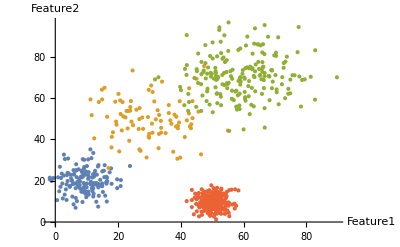

```mathematica
SeedRandom[3523] (* Initialise Random Number Generator *)
means = {{10,20},{30,50},{60,70}, {50,10}}; (* Select the centroids *)
kk = 4; (* define the number of clusters *)
dd = 2; (* define the number of features *)
nums = {150,90,200, 250}; (* define the number of samples in each cluster *)
stds =
 {5,10,10,3}; (* define the standard deviation in each cluster *) 
rN[m_,s_] := Random[NormalDistribution[m,s]]
makePoint[mean_,std_] := {rN[mean[[1]],std], rN[mean[[2]],std]}
pts = Table[Table[makePoint[means[[k]],stds[[k]]], nums[[k]]],{k,1,kk}];
ListPlot[pts, AxesLabel->{"Feature1","Feature2"}]
```